```mathematica
Predicting Bitcoin Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

- Metcalfe's law.

## Resources

- Bitcoin active addresses: bitinfocharts.com.

- Bitcoin market capitalization: bitinfocharts.com.

- Bitcoin hourly price: Recent (2024) data - bitstamp.com.

- Bitcoin circulating supply: https://www.blockchain.com/charts/total-bitcoins.

## In This Notebook

LPPLS model implementation (2025 ed.).

```mathematica
base=DirectoryName[NotebookFileName[]];
firstPriceDate="2025-03-01"
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2025-03-01

2025-12-24

```mathematica
hourlyPricesUrl="https://www.cryptodatadownload.com/cdd/Bitstamp_BTCUSD_1h.csv";
prices =Import[hourlyPricesUrl, HeaderLines->1]
```

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, -1], "ISODate"]==lastPriceDate, lastDownloadedTime=="00:00:00"}
```

{2025-05-31,00:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[closingPricesFilter, First]
```

```mathematica
Length[hourlyPrices]
```

61727

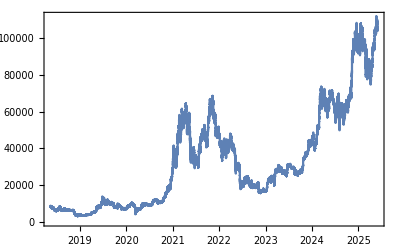

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"Bitcoin_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/Bitcoin_price-hourly-20250301-20250530.csv

```mathematica
(* Prices list. Pre-processed for performance: *)
hourlyPricesList = Import[base<>"Bitcoin_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv"]
```

```mathematica
(* Convert to market capitalization, using circulating supply data, from blockchain.info *)
(* Load circulating supply data: https://www.blockchain.com/charts/total-bitcoins *)
supplyJsonData = Import["https://api.blockchain.info/charts/total-bitcoins?timespan=all&sampled=true&metadata=false&daysAverageString=1d&cors=true&format=json"];
```

```mathematica
supplyJson=supplyJsonData[[6]][[2]]
```

```mathematica
supplyTs=supplyJson[[All, 1]][[All,2]];
supplyQuantity=supplyJson[[All, 2]][[All,2]];
```

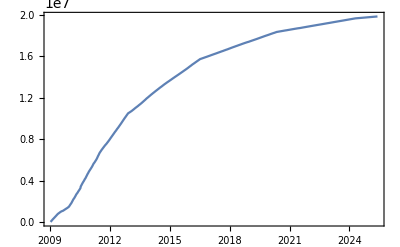

```mathematica
supplyTimestamps=MapThread[{#1, #2}&,{supplyTs, supplyQuantity}];
DateListPlot[supplyTimestamps,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Create an interpolating function from it *)
supplyFunction=Block[{},Off[ InterpolatingFunction::dmval];Interpolation[supplyTimestamps]]
```

InterpolatingFunction[…]

```mathematica
{supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}
```

{1231568277,1748345349}

```mathematica
{hourlyPricesList[[1]][[1]],hourlyPricesList[[-1]][[1]]}
```

{1526364000,1748649600}

```mathematica
{supplyFunction[hourlyPricesList[[1]][[1]]], supplyFunction[hourlyPricesList[[-3]][[1]]]}
```

{1.70345×10^7,1.98723×10^7}

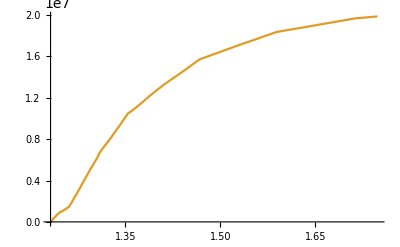

```mathematica
Plot[{,supplyFunction[i]}, {i, supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}]
```

```mathematica
(* Generate hourly market capitalization data *)
hourlyMarketCap={#[[1]], #[[2]]*supplyFunction[#[[1]]]}&/@hourlyPricesList
```

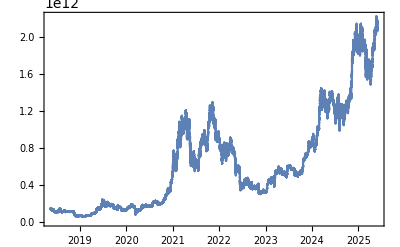

```mathematica
DateListPlot[hourlyMarketCap, DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Use the Log Market Cap *)
logMarketCap= {#[[1]], Log[#[[2]]]}&/@hourlyMarketCap
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2024 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2025-03-11", lastPriceDate},{"2025-04-07", lastPriceDate}}
```

{{2025-03-11,2025-05-30},{2025-04-07,2025-05-30}}

```mathematica
bubbleN=Length[bubblesDate]
```

2

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1741644000,1748556000},{1743976800,1748556000}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{80,53}

```mathematica
bubbles=Table[Select[logMarketCap,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1741644000,28.0867},{1743976800,28.0675}}

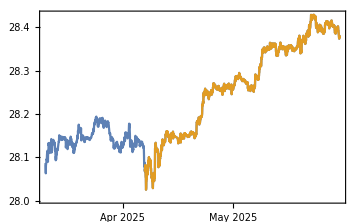

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.0984,0.868372},{1.15636,0.868372}}

```mathematica
Length/@bubblesScaled
```

{1901,1253}

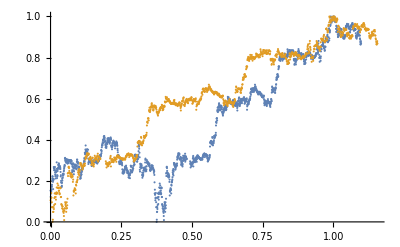

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"bubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/Bitcoin/bubbleScaled-1.tsv,/Users/mauro/Projects/Bitcoin/bubbleScaled-2.tsv}

```mathematica
(* Get params from R: *)
(*bestSpan=0.088*)
bestSpan=0.12
```

0.12

```mathematica
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{13.0746,1883.75},{13.1397,1235.67}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{2.41012,0.0357763,0.002824},{0.941663,0.0276141,0.00268683}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

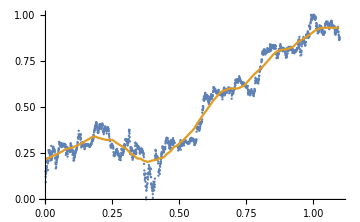
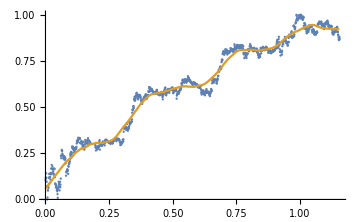

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

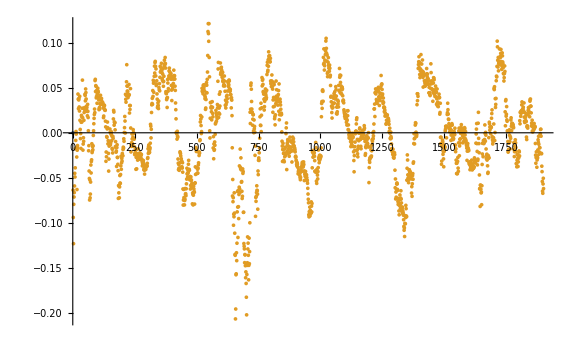
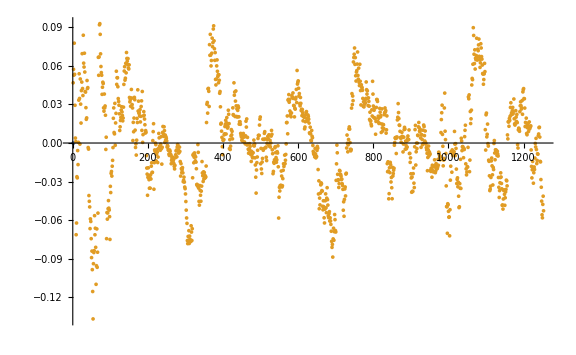

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.0471779,0.0345315}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{4.22911,1.49555}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{4.22911 > 2.41012,1.49555 > 0.941663}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.0473295,0.0347308}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0473295 > 0.0357763,0.0347308 > 0.0276141}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.0357295,0.0275589}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0473819,0.0347896}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0473819 > 0.0357763,0.0347896 > 0.0276141}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.035769,0.0276056}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble: *)
bubble=1
```

```mathematica
(* Select last bubble: *)
bubble=Length[bubbles]
```

2

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{13.1397,1235.67}

```mathematica
(* Profiling over 0.1 < m < 0.9, 5 < ω < 15 and 1. < tc < 3 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=2;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.15636

3.28844

```mathematica
(* Define 3 days resolution scaled interval step: *)
stepTc=3/bubblesDays[[bubble]]//N
```

0.0566038

```mathematica
(* Define 3 days resolution scaled initial time step *)
stepTi=3/bubblesDays[[bubble]]//N
```

0.0566038

```mathematica
(* Slow. Shortcut below *)
fits=Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

{1896.47,{{a→27.046,b→-24.6395,c→-0.733091,d→-0.0430374,T_1→0.,tc→3.2508,m→0.1,ω→3.,RSS→3.29569,ℛerror→0.00264502,ℛσ→0.0513063,LL→3780.47,ρ→0.971961,σ→-0.0120595,μ→1.4447×10^-16},{a→5.38711,b→-4.87286,c→-0.468858,d→0.584504,T_1→0.0566038,tc→3.2508,m→0.1,ω→3.,RSS→3.00345,ℛerror→0.00253884,ℛσ→0.0502596,LL→3677.6,ρ→0.973426,σ→-0.0115047,μ→-6.19515×10^-17},{a→1.11685,b→-0.655722,c→-0.0232115,d→-0.079018,T_1→0.113208,tc→1.32627,m→1.,ω→13.4,RSS→1.75915,ℛerror→0.00156927,ℛσ→0.0395084,LL→3609.01,ρ→0.964117,σ→-0.0104839,μ→1.77681×10^-17},{a→1.1195,b→-0.660453,c→-0.025051,d→-0.0809941,T_1→0.169811,tc→1.32627,m→1.,ω→13.7,RSS→1.67319,ℛerror→0.00157997,ℛσ→0.0396367,LL→3426.19,ρ→0.964929,σ→-0.0104002,μ→-1.30434×10^-17},{a→29.3728,b→-27.3255,c→-0.65723,d→0.275539,T_1→0.226415,tc→2.62816,m→0.1,ω→3.,RSS→2.64381,ℛerror→0.00260218,ℛσ→0.0508616,LL→3297.33,ρ→0.980395,σ→-0.010017,μ→-2.01127×10^-17},{a→1.11909,b→-0.659624,c→-0.0177891,d→-0.0797857,T_1→0.283019,tc→1.32627,m→1.,ω→13.5,RSS→1.64568,ℛerror→0.00172503,ℛσ→0.0414035,LL→3073.94,ρ→0.966419,σ→-0.010634,μ→-5.78059×10^-18},{a→1.87783,b→-1.17734,c→-0.109271,d→-0.108591,T_1→0.339623,tc→1.49609,m→0.1,ω→3.,RSS→1.56229,ℛerror→0.00175145,ℛσ→0.0417103,LL→2877.19,ρ→0.96816,σ→-0.0104357,μ→1.06718×10^-17},{a→-1.35066,b→2.11579,c→-0.07857,d→-0.293804,T_1→0.396226,tc→1.6659,m→0.1,ω→3.,RSS→1.51212,ℛerror→0.00182184,ℛσ→0.0425295,LL→2694.03,ρ→0.973286,σ→-0.00975877,μ→1.47265×10^-17},{a→-2.27297,b→2.97729,c→0.0686897,d→-0.356875,T_1→0.45283,tc→1.77911,m→0.1,ω→3.,RSS→1.47256,ℛerror→0.0019199,ℛσ→0.0436463,LL→2479.19,ρ→0.973676,σ→-0.00994219,μ→-1.13202×10^-17},{a→0.54236,b→0.116933,c→0.116844,d→-0.26317,T_1→0.509434,tc→1.77911,m→0.1,ω→3.,RSS→1.44678,ℛerror→0.00205217,ℛσ→0.0451093,LL→2271.94,ρ→0.974543,σ→-0.0101064,μ→-3.85039×10^-18}}}

```mathematica
(* Shortcut: *)
fits=;
```

```mathematica
(* Timing in minutes: *)
fits[[1]]/60
```

31.6078

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→3.70363 | ℛσ→0.0512824 | LL→3780.48
T_1→0.0566038 | tc→3.76024 | ℛσ→0.0502558 | LL→3677.61
T_1→0.113208 | tc→1.32627 | ℛσ→0.0395084 | LL→3609.01
T_1→0.169811 | tc→1.32627 | ℛσ→0.0396367 | LL→3426.19
T_1→0.226415 | tc→2.62816 | ℛσ→0.0508616 | LL→3297.33
T_1→0.283019 | tc→1.32627 | ℛσ→0.0414035 | LL→3073.94
T_1→0.339623 | tc→1.49609 | ℛσ→0.0417103 | LL→2877.19
T_1→0.396226 | tc→1.6659 | ℛσ→0.0425295 | LL→2694.03
T_1→0.45283 | tc→1.77911 | ℛσ→0.0436463 | LL→2479.19
T_1→0.509434 | tc→1.77911 | ℛσ→0.0451093 | LL→2271.94

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

2.07911

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.32627

3.76024

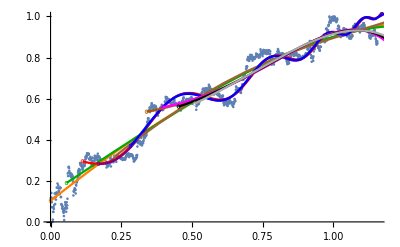

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.0566038,0.113208,0.169811,0.226415,0.283019,0.339623,0.396226,0.45283,0.509434}

{0.00264255,0.00253845,0.00156927,0.00157997,0.00260218,0.00172503,0.00175145,0.00182184,0.0019199,0.00205217}

{3.29261,3.00299,1.75915,1.67319,2.64381,1.64568,1.56229,1.51212,1.47256,1.44678}

{0.0512824,0.0502558,0.0395084,0.0396367,0.0508616,0.0414035,0.0417103,0.0425295,0.0436463,0.0451093}

```mathematica
Export[base<>"t1s.tsv", Join[{{"t1"}},T1s]]
```

/Users/mauro/Projects/Bitcoin/t1s.tsv

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

Part::pkspec1: The expression {{1743976800,28.0675},{1743980400,28.0724},{1743984000,28.0713},{1743987600,28.082},{1743991200,28.0729},{1743994800,28.0638},{1743998400,28.0542},{1744002000,28.0537},{1744005600,28.0252},{1744009200,28.0295},«1243»} cannot be used as a part specification.

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

1205

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

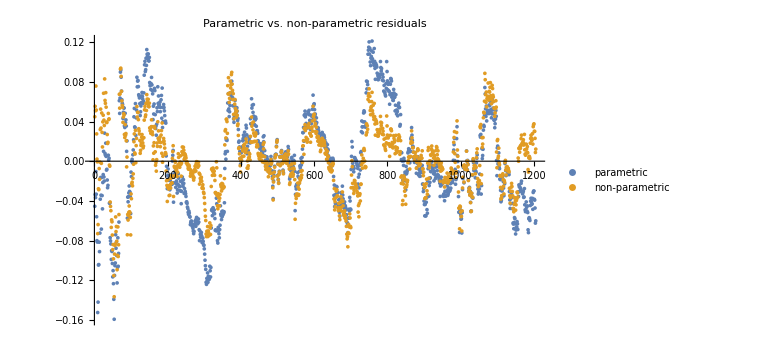

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{1.39051,2.92677}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.034217,0.0494272}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.0011708,0.00244305}

```mathematica
selN=Length[T1s];
selN
```

10

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{1205,1135,1064,993,922,851,780,709,638,568}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{1205,1135,1064,993,922,851,780,709,638,568}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"selBubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{1205,1135,1064,993,922,851,780,709,638,568}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.00244305,0.0025296,0.00135756,0.00141539,0.0014734,0.00154127,0.00100201,0.00103699,0.000992047,0.00089506}

```mathematica
RSSs
```

{2.92677,2.86604,1.44988,1.41964,1.41299,1.37789,0.830669,0.793297,0.694433,0.568363}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.0339514,0.0315135,0.0307113,0.0307439,0.0317842,0.0307328,0.0295883,0.0305738,0.031606,0.0322086}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.937038,σ→-0.0118518,μ→0.0000934865},{ρ→0.942058,σ→-0.0105665,μ→0.000124771},{ρ→0.946147,σ→-0.00993774,μ→0.0000687942},{ρ→0.949291,σ→-0.00966098,μ→0.0000190162},{ρ→0.951601,σ→-0.00976317,μ→0.0000346184},{ρ→0.947687,σ→-0.00980422,μ→0.00018943},{ρ→0.944714,σ→-0.00969566,μ→0.0000583277},{ρ→0.946213,σ→-0.00988499,μ→0.0000323387},{ρ→0.949099,σ→-0.00994736,μ→0.0000915755},{ρ→0.947757,σ→-0.0102653,μ→-0.000048789}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[0.0000934865,{0.937038},0.000140465],ARProcess[0.000124771,{0.942058},0.000111652],ARProcess[0.0000687942,{0.946147},0.0000987587],ARProcess[0.0000190162,{0.949291},0.0000933345],ARProcess[0.0000346184,{0.951601},0.0000953195],ARProcess[0.00018943,{0.947687},0.0000961226],ARProcess[0.0000583277,{0.944714},0.0000940057],ARProcess[0.0000323387,{0.946213},0.000097713],ARProcess[0.0000915755,{0.949099},0.0000989499],ARProcess[-0.000048789,{0.947757},0.000105376]}

{3639.86,3585.85,3407.48,3197.72,2959.26,2729.59,2511.58,2267.6,2035.56,1794.62}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
(* Allowing for the distribution of the residual standard error on different window sizes to be approximated by Monte Carlo. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

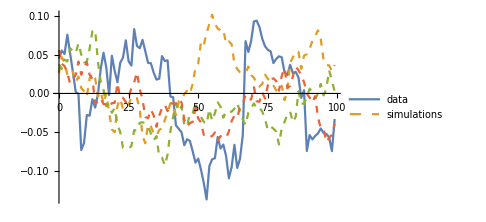
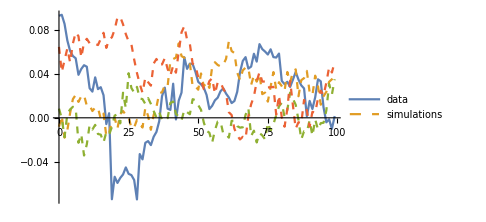
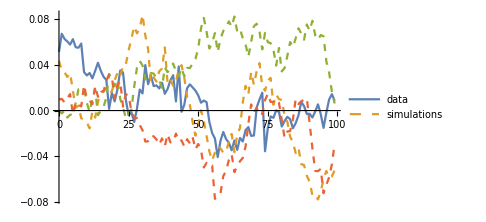
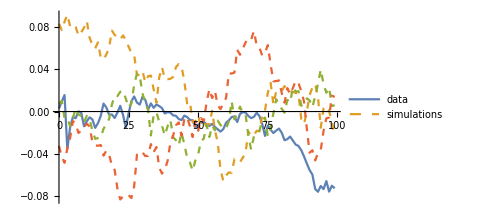
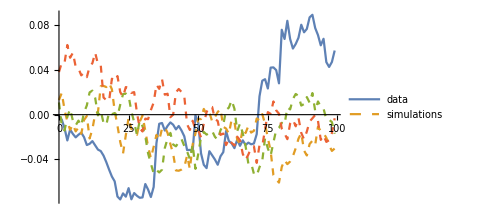
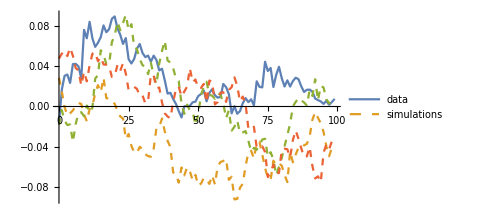
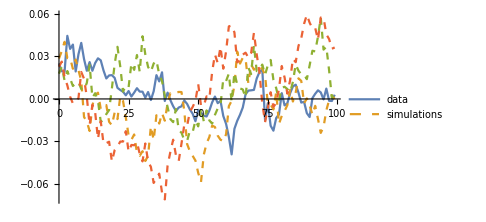
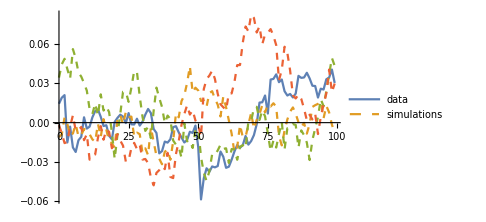

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{13.15,1187.66},{13.0626,1117.77},{13.2449,1046.53},{13.1797,975.62},{13.1414,904.671},{13.0808,833.752},{13.2799,762.493},{13.219,691.574},{13.1667,620.644},{13.1028,550.73}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

1187.66

13.15

{1187.66,1117.77,1046.53,975.62,904.671,833.752,762.493,691.574,620.644,550.73}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 1.11525 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 1.11534 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 142570 Kb

Memory Used: 0.979493 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{0,0,30,15,34,11,257,314,529,723}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.,0.,0.03,0.015,0.034,0.011,0.257,0.314,0.529,0.723}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True,True,False,False,False,False}

```mathematica
(* Take the largest that is not rejected *)
largestNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

7

```mathematica
(* Take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
```

1.11283

```mathematica
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

3

```mathematica
index=If[NumericQ[largestNotRejectedIndex], largestNotRejectedIndex,minTcIndex]
```

7

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→1.18152,b→-0.656677,c→0.0630457,d→0.00391122,T_1→0.352941,tc→1.40694,m→1.,ω→13.8,RSS→0.830669,ℛerror→0.00100201,ℛσ→0.0315407,LL→2697.38,ρ→0.951595,σ→-0.00968836,μ→-8.03532×10^-18,index→7}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

7

{a→1.18152,b→-0.656677,c→0.0630457,d→0.00391122,T_1→0.352941,tc→1.40694,m→1.,ω→13.8,RSS→0.830669,ℛerror→0.00100201,ℛσ→0.0315407,LL→2697.38,ρ→0.951595,σ→-0.00968836,μ→-8.03532×10^-18}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

1.

13.8

1.40694

2697.38

```mathematica
t1=Subscript[T, 1]/.fit
```

0.352941

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

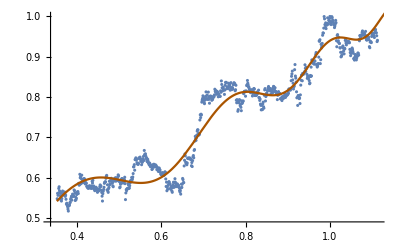

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→1.18152,b→-0.656677,c→0.0630457,d→0.00391122,T_1→0.352941,tc→1.40694,m→1.,ω→13.8,RSS→0.830669,ℛerror→0.00100201,ℛσ→0.0315407,LL→2697.38,ρ→0.951595,σ→-0.00968836,μ→-8.03532×10^-18}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.951595,σ→-0.00968836,μ→-8.03532×10^-18}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

1.92006

{1.39382,1.40694}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92001

{1.39382,1.40694,1.42169}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.11273

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Mon 9 Jun 2025 21:11:51

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Tue 10 Jun 2025 11:38:21

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Wed 11 Jun 2025 03:51:14

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Thu 12 Jun 2025 08:56:00

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Tue 2 Sep 2025 01:31:18

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Wed 28 May 2025 00:06:36

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Mon 7 Apr 2025 00:00:00 | tc→1.17165 | Fri 30 May 2025 16:48:57
T_1→0.0588235 | Wed 9 Apr 2025 16:42:21 | tc→3.23047 | Tue 2 Sep 2025 01:31:18
T_1→0.117647 | Sat 12 Apr 2025 09:24:42 | tc→1.11283 | Wed 28 May 2025 00:06:36
T_1→0.176471 | Tue 15 Apr 2025 02:07:03 | tc→1.11283 | Wed 28 May 2025 00:06:36
T_1→0.235294 | Thu 17 Apr 2025 18:49:24 | tc→1.11283 | Wed 28 May 2025 00:06:36
T_1→0.294118 | Sun 20 Apr 2025 11:31:45 | tc→1.11283 | Wed 28 May 2025 00:06:36
T_1→0.352941 | Wed 23 Apr 2025 04:14:07 | tc→1.40694 | Tue 10 Jun 2025 11:38:21
T_1→0.411765 | Fri 25 Apr 2025 20:56:28 | tc→1.40694 | Tue 10 Jun 2025 11:38:21
T_1→0.470588 | Mon 28 Apr 2025 13:38:49 | tc→1.40694 | Tue 10 Jun 2025 11:38:21
T_1→0.529412 | Thu 1 May 2025 06:21:10 | tc→1.40694 | Tue 10 Jun 2025 11:38:21

```mathematica
(* Compute market cap at the low leg of the best Tc: *)
bestM=bestLppls[bestTc-epsilon,bestTc]
```

1.18145

```mathematica
lowCIM=bestLppls[lowCItc,bestTc]
```

1.17208

```mathematica
lastScaledM=bubbleBest[[-1]][[2]]
```

0.940834

```mathematica
lastPriceDate
```

2025-05-28

```mathematica
(* Closing market cap at lastPriceDate date (`$lastPriceDate`) (https://coinmarketcap.com/currencies/bitcoin/historical-data/https://coinmarketcap.com/currencies/bitcoin/historical-data/Nonehttps://coinmarketcap.com/currencies/bitcoin/historical-data/HyperlinkActionRecycledHyperlinkActive) (Millions of USD): *)
(* Automated download *)
timeStartTs=UnixTime[lastPriceDate];
timeEndTs=timeStartTs+86400;
latestMarketCapUrl="https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart="<>ToString[timeStartTs]<>"&timeEnd="<>ToString[timeEndTs]<>"&interval=1d"
```

https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart=1748383200&timeEnd=1748469600&interval=1d

```mathematica
latestMarketCapData=Import[latestMarketCapUrl]
```

{data→{id→1,name→Bitcoin,symbol→BTC,timeEnd→1713916799,quotes→{{timeOpen→2025-05-28T00:00:00.000Z,timeClose→2025-05-28T23:59:59.999Z,timeHigh→2025-05-28T01:01:00.000Z,timeLow→2025-05-28T20:03:00.000Z,quote→{name→2781,open→108992.,high→109298.,low→106813.,close→107802.,volume→4.915537749262×10^10,marketCap→2.14203230075099×10^12,timestamp→2025-05-28T23:59:59.999Z}}}},status→{timestamp→2025-05-29T09:38:52.890Z,error_code→0,error_message→SUCCESS,elapsed→57,credit_count→0}}

```mathematica
latestMarketCap=Flatten[latestMarketCapData[[1]][[2]][[5]][[2]]][[5]][[2]][[7]][[2]]/10^7
```

214203.230075099

```mathematica
(* Plot predicted market cap evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVM[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestMarketCap/Exp[lastScaledM]]]<>"M"},{i,min, max,1}]
```

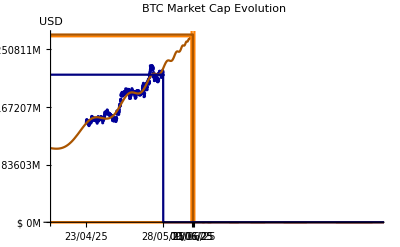

```mathematica
marketCapPrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Market Cap Evolution",PlotRange->{{0,maxTc},{0,Exp[bestM]}}, Ticks->{ticksH,ticksVM},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestM+1],UnitStep[ti-highCItc]Exp[bestM+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIM],UnitStep[bestTc-ti]Exp[bestM],UnitStep[lastScaledTc-ti]Exp[lastScaledM]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"BTC_MarketCapPrediction-"<>lastPriceDate<>".png",marketCapPrediction]
```

/Users/mauro/Projects/Bitcoin/BTC_MarketCapPrediction-2025-05-28.png

```mathematica
mToMarketCap[m_]:= latestMarketCap/Exp[lastScaledM] Exp[m]
```

```mathematica
lowCIMarketCap=mToMarketCap[lowCIM]
```

269931.

```mathematica
bestMarketCap=mToMarketCap[bestM]
```

272473.

```mathematica
(* The price is the ratio of the market cap (in Millions USD) to the (predicted) supply at the date: *)
mToPrice[m_, date_]:=mToMarketCap[m]10^7/supplyFunction[UnixTime[date]]
```

```mathematica
tcToDate[tc_]:= DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]tc/lastScaledTc]
```

```mathematica
(* Check: *)
lastPrice=mToPrice[lastScaledM,tcToDate[lastScaledTc]]
```

107798.

```mathematica
lowCIPrice=mToPrice[lowCIM, tcToDate[lowCItc]]
```

135800.

```mathematica
bestPrice=mToPrice[bestM, tcToDate[bestTc]]
```

137076.

```mathematica
(* Plot predicted price evolution (USD) :*)
ticksVPrice[min_,max_]:=Table[{i,"$"<>ToString[IntegerPart[i]]},{i,min, max,50000}]
```

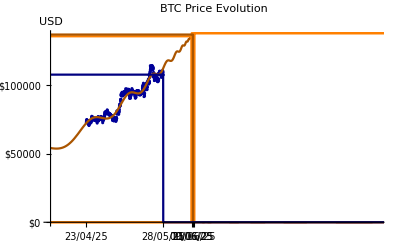

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], mToPrice[#[[2]], tcToDate[#[[1]]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Price Evolution",PlotRange->{{0,maxTc},{0,bestPrice}}, Ticks->{ticksH,ticksVPrice},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[mToPrice[lpplsModel/.fit, tcToDate[ti]]],UnitStep[ti-lowCItc](bestPrice+1000),UnitStep[ti-highCItc](bestPrice+1000)/.fit, UnitStep[lowCItc-ti]lowCIPrice,UnitStep[bestTc-ti]bestPrice,UnitStep[lastScaledTc-ti]lastPrice}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_PricePrediction-2025-05-28.png